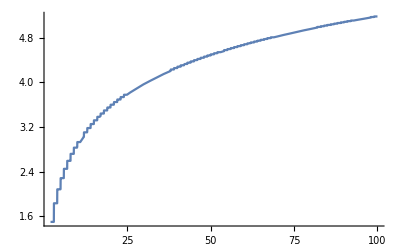

```mathematica
(*1*)
Plot[Sum[1/n,{n,m}],{m,2,100},PlotRange->All]
```

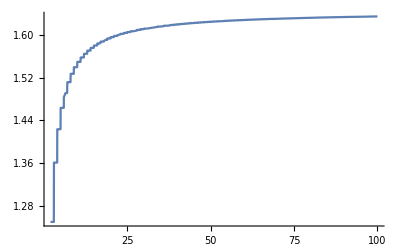

```mathematica
Plot[Sum[1/n^2,{n,m}],{m,2,100},PlotRange->All]
```

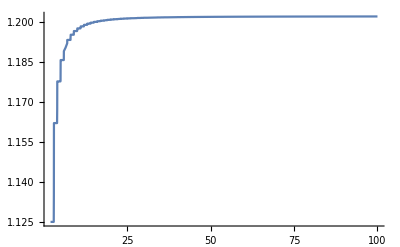

```mathematica
Plot[Sum[1/n^3,{n,m}],{m,2,100},PlotRange->All]
```

```mathematica
(*2*)
Clear["`*"]
f[x_]:=ArcTan[x];
(*在x=1处展开*)
 g[n_]:=Normal[Series[f[x],{x,1,n}]]/.x->2
data=Table[{n,N[g[n]],N[f[2]],N[Abs[f[2]-g[n]]/g[n]]*100},{n,1,9,1}];
TableForm[data,TableSpacing->{1,5},TableHeadings->{None,{"展开级数n","在x=1处展开的幂级数的值","f(1)","Error(%)"}}]
```

展开级数n | 在x=1处展开的幂级数的值 | f(1) | Error(%)
1 | 1.2854 | 1.10715 | 13.8673
2 | 1.0354 | 1.10715 | 6.92975
3 | 1.11873 | 1.10715 | 1.03535
4 | 1.11873 | 1.10715 | 1.03535
5 | 1.09373 | 1.10715 | 1.22674
6 | 1.11456 | 1.10715 | 0.665382
7 | 1.10564 | 1.10715 | 0.136795
8 | 1.10564 | 1.10715 | 0.136795
9 | 1.10911 | 1.10715 | 0.176697

```mathematica
(*在x=2处展开*)
 g[n_]:=Normal[Series[f[x],{x,2,n}]]/.x->3
data=Table[{n,N[g[n]],N[f[3]],N[Abs[f[3]-g[n]]/g[n]]*100},{n,1,9,1}];
TableForm[data,TableSpacing->{1,5},TableHeadings->{None,{"展开级数n","在x=2处展开的幂级数的值","f(3)","Error(%)"}}]
```

展开级数n | 在x=2处展开的幂级数的值 | f(3) | Error(%)
1 | 1.30715 | 1.24905 | 4.44501
2 | 1.22715 | 1.24905 | 1.78438
3 | 1.25648 | 1.24905 | 0.591833
4 | 1.24688 | 1.24905 | 0.173531
5 | 1.24951 | 1.24905 | 0.0368369
6 | 1.24904 | 1.24905 | 0.000724927
7 | 1.24898 | 1.24905 | 0.0049707
8 | 1.24909 | 1.24905 | 0.00363759
9 | 1.24902 | 1.24905 | 0.00182326

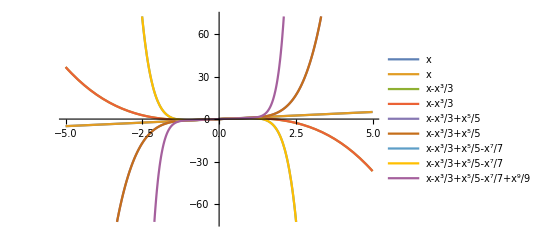

```mathematica
Plot[Evaluate[Table[Normal[Series[f[x],{x,0,n}]],{n,9}]],{x,-5,5},PlotLegends->"Expressions"]
```

```mathematica
Clear["`*"]
f[x_]:=ArcCos[x];
(*在x=0处展开*)
 g[n_]:=Normal[Series[f[x],{x,0,n}]]/.x->0.01
data=Table[{n,N[g[n]],N[f[0.01]],N[Abs[f[0.01]-g[n]]/g[n]]*100},{n,1,9,1}];
TableForm[data,TableSpacing->{1,5},TableHeadings->{None,{"展开级数n","在x=0处展开的幂级数的值","f(0.01)","Error(%)"}}]
```

展开级数n | 在x=0处展开的幂级数的值 | f(0.01) | Error
1 | 1.5608 | 1.5608 | 0.0000106788
2 | 1.5608 | 1.5608 | 0.0000106788
3 | 1.5608 | 1.5608 | 4.80552×10^-10
4 | 1.5608 | 1.5608 | 4.80552×10^-10
5 | 1.5608 | 1.5608 | 2.84527×10^-14
6 | 1.5608 | 1.5608 | 2.84527×10^-14
7 | 1.5608 | 1.5608 | 0.
8 | 1.5608 | 1.5608 | 0.
9 | 1.5608 | 1.5608 | 0.

展开级数n | 在x=1处展开的幂级数的值 | f(1.01) | Error(%)
1 | 0.+0.141421 ⅈ | 0.+0.141304 ⅈ | 0.-0.0831464 ⅈ
2 | 0.+0.141304 ⅈ | 0.+0.141304 ⅈ | 0.-0.0001871 ⅈ
3 | 0.+0.141304 ⅈ | 0.+0.141304 ⅈ | 0.-5.56607×10^-7 ⅈ
4 | 0.+0.141304 ⅈ | 0.+0.141304 ⅈ | 0.-1.89348×10^-9 ⅈ
5 | 0.+0.141304 ⅈ | 0.+0.141304 ⅈ | 0.-6.99273×10^-12 ⅈ
6 | 0.+0.141304 ⅈ | 0.+0.141304 ⅈ | 0.-1.96425×10^-14 ⅈ
7 | 0.+0.141304 ⅈ | 0.+0.141304 ⅈ | 0.+0. ⅈ
8 | 0.+0.141304 ⅈ | 0.+0.141304 ⅈ | 0.+0. ⅈ
9 | 0.+0.141304 ⅈ | 0.+0.141304 ⅈ | 0.-1.96425×10^-14 ⅈ

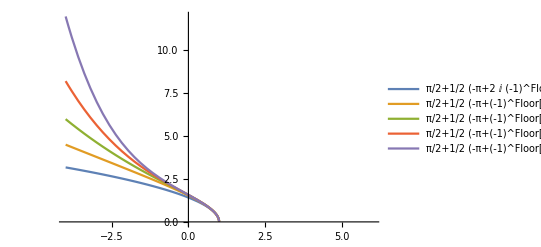

```mathematica
(*在x=1处展开*)
f[x_]:=ArcCos[x];
 g[n_]:=Normal[Series[f[x],{x,1,n}]]/.x->1.01
data=Table[{n,N[g[n]],N[f[1.01]],N[Abs[f[1.01]-g[n]]/g[n]]*100},{n,1,9,1}];
TableForm[data,TableSpacing->{1,5},TableHeadings->{None,{"展开级数n","在x=1处展开的幂级数的值","f(1.01)","Error(%)"}}]
Plot[Evaluate[Table[Normal[Series[f[x],{x,1,n}]],{n,5}]],{x,-4,6},PlotLegends->"Expressions"]
```

展开级数n | 在x=0处展开的幂级数的值 | f(0.01) | Error(%)
1 | 1. | 1.0001 | 0.01
2 | 1.0001 | 1.0001 | 3.33256×10^-11
3 | 1.0001 | 1.0001 | 3.33256×10^-11
4 | 1.0001 | 1.0001 | 3.33256×10^-11
5 | 1.0001 | 1.0001 | 3.33256×10^-11
6 | 1.0001 | 1.0001 | 0.
7 | 1.0001 | 1.0001 | 0.
8 | 1.0001 | 1.0001 | 0.
9 | 1.0001 | 1.0001 | 0.

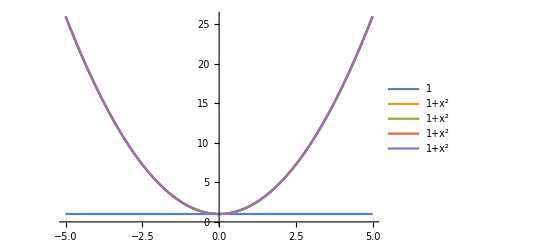

```mathematica
Clear["`*"]
(*在x=0处展开*)
f[x_]:=Exp[x^2]Cos[x^2];
 g[n_]:=Normal[Series[f[x],{x,0,n}]]/.x->0.01
data=Table[{n,N[g[n]],N[f[0.01]],N[Abs[f[0.01]-g[n]]/g[n]]*100},{n,1,9,1}];
TableForm[data,TableSpacing->{1,5},TableHeadings->{None,{"展开级数n","在x=0处展开的幂级数的值","f(0.01)","Error(%)",}}]
Plot[Evaluate[Table[Normal[Series[f[x],{x,0,n}]],{n,5}]],{x,-5,5},PlotLegends->"Expressions"]
```

展开级数n | 在x=1处展开的幂级数的值 | f(1.01) | Error(%)
1 | 1.45232 | 1.4513 | 0.0699699
2 | 1.45132 | 1.4513 | 0.00133528
3 | 1.4513 | 1.4513 | 0.0000147268
4 | 1.4513 | 1.4513 | 9.99409×10^-8
5 | 1.4513 | 1.4513 | 2.24461×10^-10
6 | 1.4513 | 1.4513 | 4.10031×10^-12
7 | 1.4513 | 1.4513 | 6.11986×10^-14
8 | 1.4513 | 1.4513 | 0.
9 | 1.4513 | 1.4513 | 0.

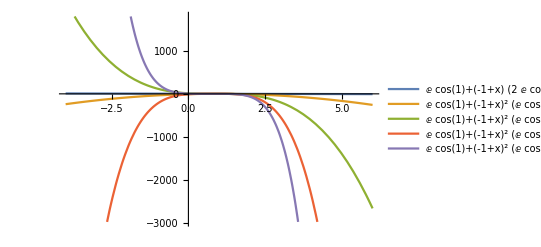

```mathematica
(*在x=1处展开*)
f[x_]:=Exp[x^2]Cos[x^2];
 g[n_]:=Normal[Series[f[x],{x,1,n}]]/.x->1.01
data=Table[{n,N[g[n]],N[f[1.01]],N[Abs[f[1.01]-g[n]]/g[n]]*100},{n,1,9,1}];
TableForm[data,TableSpacing->{1,5},TableHeadings->{None,{"展开级数n","在x=1处展开的幂级数的值","f(1.01)","Error(%)"}}]
Plot[Evaluate[Table[Normal[Series[f[x],{x,1,n}]],{n,5}]],{x,-4,6},PlotLegends->"Expressions"]
```

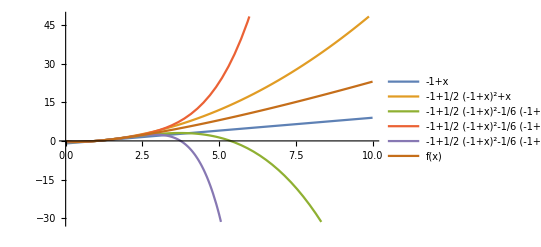

```mathematica
(*3*)
Clear["`*"]
(*在x=1处展开*)
f[x_]:=x Log[x]
Plot[{Evaluate[Table[Normal[Series[f[x],{x,1,n}]],{n,5}]],f[x]},{x,0,10},PlotLegends->"Expressions"]
```

```mathematica
(*在x=2处展开*)
```

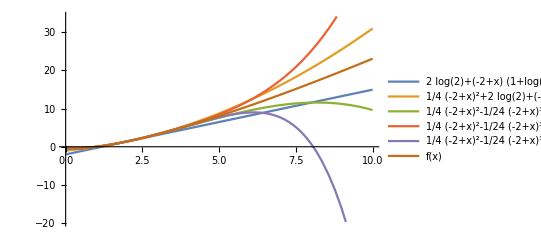

```mathematica
Plot[{Evaluate[Table[Normal[Series[f[x],{x,2,n}]],{n,5}]],f[x]},{x,0,10},PlotLegends->"Expressions"]
```

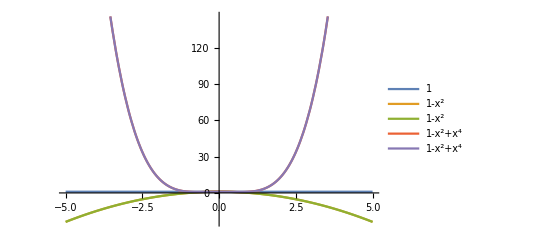

```mathematica
Clear["`*"]
(*在x=0处展开*)
f[x_]:=1/(1+x^2)
Plot[Evaluate[Table[Normal[Series[f[x],{x,0,n}]],{n,5}]],{x,-5,5},PlotLegends->"Expressions"]
```

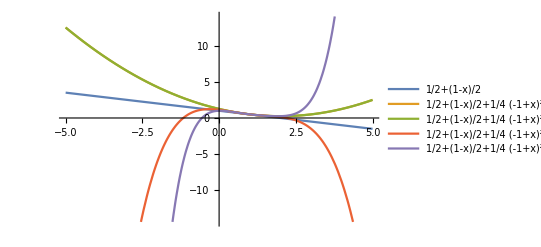

```mathematica
(*在x=1处展开*)
Plot[Evaluate[Table[Normal[Series[f[x],{x,1,n}]],{n,5}]],{x,-5,5},PlotLegends->"Expressions"]
```

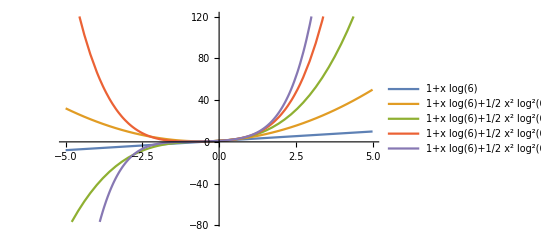

```mathematica
Clear["`*"]
(*在x=0处展开*)
f[x_]:=6^x;
Plot[Evaluate[Table[Normal[Series[f[x],{x,0,n}]],{n,5}]],{x,-5,5},PlotLegends->"Expressions"]
```

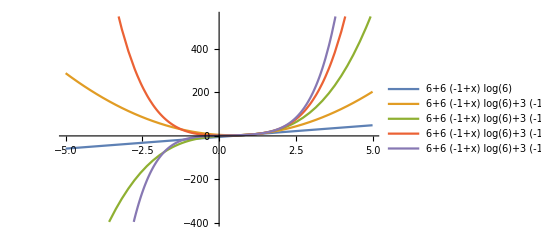

```mathematica
(*在x=1处展开*)
Plot[Evaluate[Table[Normal[Series[f[x],{x,1,n}]],{n,5}]],{x,-5,5},PlotLegends->"Expressions"]
```

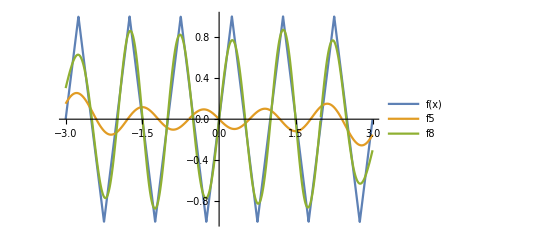

```mathematica
(*4*)
Clear["`*"]
f[x_]:=TriangleWave[x];
f5=FourierSeries[f[x],x,5];
f8=FourierSeries[f[x],x,8];
Plot[{f[x],f5,f8},{x,-3,3},PlotLegends->"Expressions"]
```

```mathematica
F=f[0.2];
value[n_]:=FourierSeries[f[x],x,n]/.x->0.2
data=Table[{n,N[value[n]],N[F],N[Abs[value[n]-F]/F]},{n,4,15,2}];
TableForm[data,TableSpacing->{1,5},TableHeadings->{None, {"傅里叶级数","x=0.2的级数值","f（0.2）","Error"}}]
```

傅里叶级数 | x=0.2的级数值 | f（0.2） | Error
4 | -63.1296+0. ⅈ | 0.961538 | 66.6548
6 | -289.498+7.32747×10^-15 ⅈ | 0.961538 | 302.078
8 | -388.847+0. ⅈ | 0.961538 | 405.401
10 | 10618.4+2.27374×10^-13 ⅈ | 0.961538 | 11042.2
12 | 165869.+2.34701×10^-13 ⅈ | 0.961538 | 172503.
14 | 1.67809×10^6-3.6593×10^-12 ⅈ | 0.961538 | 1.74521×10^6

ⅇ^(-Abs[ω]) √(π/2)

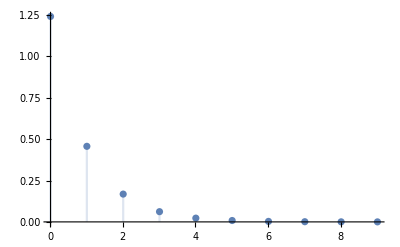

```mathematica
f=FourierTransform[f[x],x,ω]
DiscretePlot[Abs[f],{ω,0.01,10}]
```

```mathematica
Clear["'*"]
f[x_]:=Which[-1/2≤x<1/2,1-x^2]
f[x_]:=f[x-1]/;x≥1/2
f[x_]:=f[x+1]/;x<=-1/2
f5=FourierSeries[f[x],x,5];
f8=FourierSeries[f[x],x,8];
Plot[{f[x],f5,f8},{x,-3,3},PlotLegends->"Expressions"]
```

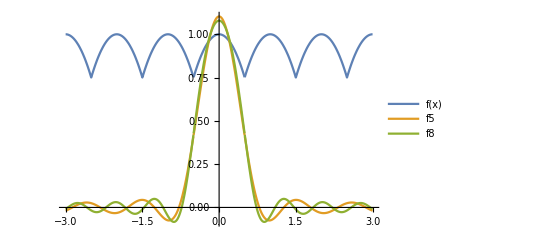

```mathematica
F=f[0.2];
value[n_]:=FourierSeries[f[x],x,n]/.x->0.2
data=Table[{n,N[value[n]],N[F],N[Abs[value[n]-F]/F]},{n,4,15,2}];
TableForm[data,TableSpacing->{1,5},TableHeadings->{None, {"傅里叶级数","x=0.2的级数值","f（0.2）","Error"}}]
```

傅里叶级数 | x=0.2的级数值 | f（0.2） | Error
4 | 0.915601+0. ⅈ | 0.96 | 0.0462489
6 | 0.97151+0. ⅈ | 0.96 | 0.0119897
8 | 0.970474+0. ⅈ | 0.96 | 0.0109103
10 | 1.00258+0. ⅈ | 0.96 | 0.0443552
12 | 1.03468+0. ⅈ | 0.96 | 0.0777865
14 | 1.01186+6.93889×10^-18 ⅈ | 0.96 | 0.0540194

(-4 ω Cos[ω/2]+(8+3 ω^2) Sin[ω/2])/(2 √(2 π) ω^3)

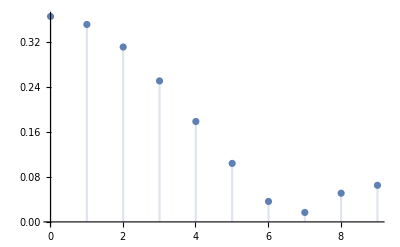

```mathematica
f=FourierTransform[f[x],x,ω]
DiscretePlot[Abs[f],{ω,0.01,10}]
```

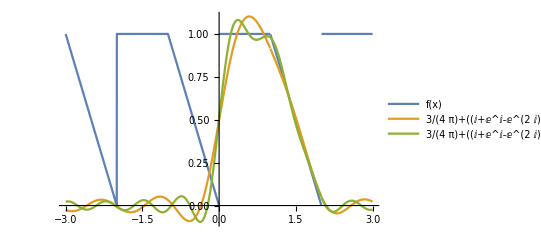

```mathematica
Clear["`*"]
f[x_]:=Piecewise[{{1,0<=x<1},{2-x,1<=x<=2}}]
f[x_]:=f[x-2]/;x>2
f[x_]:=f[x+2]/;x<0
f5=FourierSeries[f[x],x,5];
f8=FourierSeries[f[x],x,8];
Plot[{f[x],Evaluate[f5],Evaluate[f8]},{x,-3,3},PlotLegends->"Expressions"]
```

```mathematica
F=f[0.2];
value[n_]:=FourierSeries[f[x],x,n]/.x->0.2
data=Table[{n,N[value[n]],N[F],N[Abs[value[n]-F]/F]},{n,4,15,2}];
TableForm[data,TableSpacing->{1,5},TableHeadings->{None, {"傅里叶级数","x=0.2的级数值","f（0.2）","Error"}}]
```

傅里叶级数 | x=0.2的级数值 | f（0.2） | Error
4 | 0.763581+0. ⅈ | 1. | 0.236419
6 | 0.872367+0. ⅈ | 1. | 0.127633
8 | 0.961728+0. ⅈ | 1. | 0.038272
10 | 1.0284-4.33681×10^-19 ⅈ | 1. | 0.0284039
12 | 1.06592+0. ⅈ | 1. | 0.0659207
14 | 1.08412+0. ⅈ | 1. | 0.0841158

(ⅇ^(ⅈ ω)-ⅇ^(2 ⅈ ω)+ⅈ ω)/(√(2 π) ω^2)

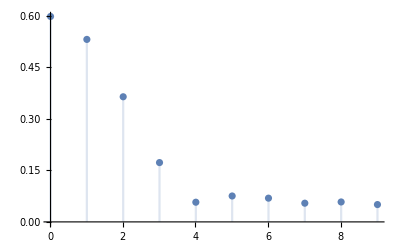

```mathematica
f=FourierTransform[f[x],x,ω]
DiscretePlot[Abs[f],{ω,0.01,10}]
```

(ⅈ (-1+ⅇ^ⅈ)^2 ⅇ^(-ⅈ+ⅈ x))/(2 π)+(ⅈ (-1+ⅇ^(2 ⅈ))^2 ⅇ^(-2 ⅈ+2 ⅈ x))/(4 π)-(ⅈ (-1+ⅇ^(3 ⅈ))^2 ⅇ^(-3 ⅈ-3 ⅈ x))/(6 π)+(ⅈ (-1+ⅇ^(3 ⅈ))^2 ⅇ^(-3 ⅈ+3 ⅈ x))/(6 π)-(ⅈ (-1+ⅇ^(4 ⅈ))^2 ⅇ^(-4 ⅈ-4 ⅈ x))/(8 π)+(ⅈ (-1+ⅇ^(4 ⅈ))^2 ⅇ^(-4 ⅈ+4 ⅈ x))/(8 π)-(ⅈ (-1+ⅇ^(5 ⅈ))^2 ⅇ^(-5 ⅈ-5 ⅈ x))/(10 π)+(ⅈ (-1+ⅇ^(5 ⅈ))^2 ⅇ^(-5 ⅈ+5 ⅈ x))/(10 π)-(ⅈ (-1+ⅇ^(6 ⅈ))^2 ⅇ^(-6 ⅈ-6 ⅈ x))/(12 π)+(ⅈ (-1+ⅇ^(6 ⅈ))^2 ⅇ^(-6 ⅈ+6 ⅈ x))/(12 π)-(ⅈ (-1+ⅇ^(7 ⅈ))^2 ⅇ^(-7 ⅈ-7 ⅈ x))/(14 π)+(ⅈ (-1+ⅇ^(7 ⅈ))^2 ⅇ^(-7 ⅈ+7 ⅈ x))/(14 π)-(ⅈ (-1+ⅇ^(8 ⅈ))^2 ⅇ^(-8 ⅈ-8 ⅈ x))/(16 π)+(ⅈ (-1+ⅇ^(8 ⅈ))^2 ⅇ^(-8 ⅈ+8 ⅈ x))/(16 π)+(2 ⅈ ⅇ^(-ⅈ x) Sin[1/2]^2)/π+((-1+ⅇ^(2 ⅈ)) ⅇ^(-ⅈ-2 ⅈ x) Sin[1])/(2 π)

(ⅈ (-1+ⅇ^ⅈ)^2 ⅇ^(-ⅈ+ⅈ x))/(2 π)+(ⅈ (-1+ⅇ^(2 ⅈ))^2 ⅇ^(-2 ⅈ+2 ⅈ x))/(4 π)-(ⅈ (-1+ⅇ^(3 ⅈ))^2 ⅇ^(-3 ⅈ-3 ⅈ x))/(6 π)+(ⅈ (-1+ⅇ^(3 ⅈ))^2 ⅇ^(-3 ⅈ+3 ⅈ x))/(6 π)-(ⅈ (-1+ⅇ^(4 ⅈ))^2 ⅇ^(-4 ⅈ-4 ⅈ x))/(8 π)+(ⅈ (-1+ⅇ^(4 ⅈ))^2 ⅇ^(-4 ⅈ+4 ⅈ x))/(8 π)-(ⅈ (-1+ⅇ^(5 ⅈ))^2 ⅇ^(-5 ⅈ-5 ⅈ x))/(10 π)+(ⅈ (-1+ⅇ^(5 ⅈ))^2 ⅇ^(-5 ⅈ+5 ⅈ x))/(10 π)-(ⅈ (-1+ⅇ^(6 ⅈ))^2 ⅇ^(-6 ⅈ-6 ⅈ x))/(12 π)+(ⅈ (-1+ⅇ^(6 ⅈ))^2 ⅇ^(-6 ⅈ+6 ⅈ x))/(12 π)-(ⅈ (-1+ⅇ^(7 ⅈ))^2 ⅇ^(-7 ⅈ-7 ⅈ x))/(14 π)+(ⅈ (-1+ⅇ^(7 ⅈ))^2 ⅇ^(-7 ⅈ+7 ⅈ x))/(14 π)-(ⅈ (-1+ⅇ^(8 ⅈ))^2 ⅇ^(-8 ⅈ-8 ⅈ x))/(16 π)+(ⅈ (-1+ⅇ^(8 ⅈ))^2 ⅇ^(-8 ⅈ+8 ⅈ x))/(16 π)-(ⅈ (-1+ⅇ^(9 ⅈ))^2 ⅇ^(-9 ⅈ-9 ⅈ x))/(18 π)+(ⅈ (-1+ⅇ^(9 ⅈ))^2 ⅇ^(-9 ⅈ+9 ⅈ x))/(18 π)-(ⅈ (-1+ⅇ^(10 ⅈ))^2 ⅇ^(-10 ⅈ-10 ⅈ x))/(20 π)+(ⅈ (-1+ⅇ^(10 ⅈ))^2 ⅇ^(-10 ⅈ+10 ⅈ x))/(20 π)-(ⅈ (-1+ⅇ^(11 ⅈ))^2 ⅇ^(-11 ⅈ-11 ⅈ x))/(22 π)+(ⅈ (-1+ⅇ^(11 ⅈ))^2 ⅇ^(-11 ⅈ+11 ⅈ x))/(22 π)+(2 ⅈ ⅇ^(-ⅈ x) Sin[1/2]^2)/π+((-1+ⅇ^(2 ⅈ)) ⅇ^(-ⅈ-2 ⅈ x) Sin[1])/(2 π)

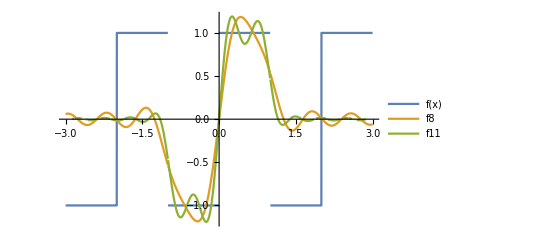

```mathematica
(*5*)
Clear["`*"]
f[x_]:=Which[-1≤x≤0,-1,0≤x≤1,1]
f[x_]:=f[x-2]/;x≥1
f[x_]:=f[x+2]/;x≤-1
f8=FourierSeries[f[x],x,8]
f11=FourierSeries[f[x],x,11]
Plot[{f[x],f8,f11},{x,-3,3},PlotLegends->"Expressions"]
```

-(ⅈ √(2/π) (-1+Cos[w]))/w

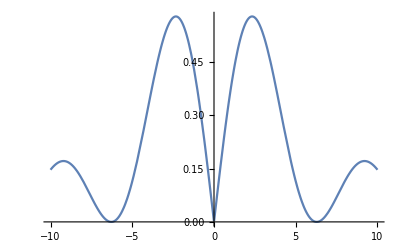

```mathematica
f=FourierTransform[f[x],x,w]
Plot[Abs[f],{w,-10,10},PlotRange->All]
```

1/π-((1-(1-2 ⅈ) ⅇ^(2 ⅈ)) ⅇ^(-ⅈ x))/(2 π)-((1-(1+2 ⅈ) ⅇ^(-2 ⅈ)) ⅇ^(ⅈ x))/(2 π)-((1-(1-4 ⅈ) ⅇ^(4 ⅈ)) ⅇ^(-2 ⅈ x))/(8 π)-((1-(1+4 ⅈ) ⅇ^(-4 ⅈ)) ⅇ^(2 ⅈ x))/(8 π)-((1-(1-6 ⅈ) ⅇ^(6 ⅈ)) ⅇ^(-3 ⅈ x))/(18 π)-((1-(1+6 ⅈ) ⅇ^(-6 ⅈ)) ⅇ^(3 ⅈ x))/(18 π)-((1-(1-8 ⅈ) ⅇ^(8 ⅈ)) ⅇ^(-4 ⅈ x))/(32 π)-((1-(1+8 ⅈ) ⅇ^(-8 ⅈ)) ⅇ^(4 ⅈ x))/(32 π)-((1-(1-10 ⅈ) ⅇ^(10 ⅈ)) ⅇ^(-5 ⅈ x))/(50 π)-((1-(1+10 ⅈ) ⅇ^(-10 ⅈ)) ⅇ^(5 ⅈ x))/(50 π)-((1-(1-12 ⅈ) ⅇ^(12 ⅈ)) ⅇ^(-6 ⅈ x))/(72 π)-((1-(1+12 ⅈ) ⅇ^(-12 ⅈ)) ⅇ^(6 ⅈ x))/(72 π)-((1-(1-14 ⅈ) ⅇ^(14 ⅈ)) ⅇ^(-7 ⅈ x))/(98 π)-((1-(1+14 ⅈ) ⅇ^(-14 ⅈ)) ⅇ^(7 ⅈ x))/(98 π)-((1-(1-16 ⅈ) ⅇ^(16 ⅈ)) ⅇ^(-8 ⅈ x))/(128 π)-((1-(1+16 ⅈ) ⅇ^(-16 ⅈ)) ⅇ^(8 ⅈ x))/(128 π)

1/π-((1-(1-2 ⅈ) ⅇ^(2 ⅈ)) ⅇ^(-ⅈ x))/(2 π)-((1-(1+2 ⅈ) ⅇ^(-2 ⅈ)) ⅇ^(ⅈ x))/(2 π)-((1-(1-4 ⅈ) ⅇ^(4 ⅈ)) ⅇ^(-2 ⅈ x))/(8 π)-((1-(1+4 ⅈ) ⅇ^(-4 ⅈ)) ⅇ^(2 ⅈ x))/(8 π)-((1-(1-6 ⅈ) ⅇ^(6 ⅈ)) ⅇ^(-3 ⅈ x))/(18 π)-((1-(1+6 ⅈ) ⅇ^(-6 ⅈ)) ⅇ^(3 ⅈ x))/(18 π)-((1-(1-8 ⅈ) ⅇ^(8 ⅈ)) ⅇ^(-4 ⅈ x))/(32 π)-((1-(1+8 ⅈ) ⅇ^(-8 ⅈ)) ⅇ^(4 ⅈ x))/(32 π)-((1-(1-10 ⅈ) ⅇ^(10 ⅈ)) ⅇ^(-5 ⅈ x))/(50 π)-((1-(1+10 ⅈ) ⅇ^(-10 ⅈ)) ⅇ^(5 ⅈ x))/(50 π)-((1-(1-12 ⅈ) ⅇ^(12 ⅈ)) ⅇ^(-6 ⅈ x))/(72 π)-((1-(1+12 ⅈ) ⅇ^(-12 ⅈ)) ⅇ^(6 ⅈ x))/(72 π)-((1-(1-14 ⅈ) ⅇ^(14 ⅈ)) ⅇ^(-7 ⅈ x))/(98 π)-((1-(1+14 ⅈ) ⅇ^(-14 ⅈ)) ⅇ^(7 ⅈ x))/(98 π)-((1-(1-16 ⅈ) ⅇ^(16 ⅈ)) ⅇ^(-8 ⅈ x))/(128 π)-((1-(1+16 ⅈ) ⅇ^(-16 ⅈ)) ⅇ^(8 ⅈ x))/(128 π)-((1-(1-18 ⅈ) ⅇ^(18 ⅈ)) ⅇ^(-9 ⅈ x))/(162 π)-((1-(1+18 ⅈ) ⅇ^(-18 ⅈ)) ⅇ^(9 ⅈ x))/(162 π)-((1-(1-20 ⅈ) ⅇ^(20 ⅈ)) ⅇ^(-10 ⅈ x))/(200 π)-((1-(1+20 ⅈ) ⅇ^(-20 ⅈ)) ⅇ^(10 ⅈ x))/(200 π)-((1-(1-22 ⅈ) ⅇ^(22 ⅈ)) ⅇ^(-11 ⅈ x))/(242 π)-((1-(1+22 ⅈ) ⅇ^(-22 ⅈ)) ⅇ^(11 ⅈ x))/(242 π)

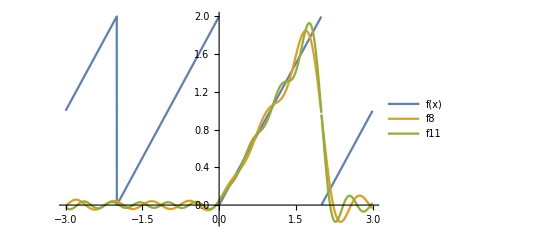

```mathematica
Clear["`*"]
f[x_]:=Which[0≤x≤2,x]
f[x_]:=f[x-2]/;x≥2
f[x_]:=f[x+2]/;x≤0
f8=FourierSeries[f[x],x,8]
f11=FourierSeries[f[x],x,11]
Plot[{f[x],f8,f11},{x,-3,3},PlotLegends->"Expressions"]
```

```mathematica
f=FourierTransform[f[x],x,w]
```

FourierTransform[(-1+ⅇ^(2 ⅈ w) (1-2 ⅈ w))/(√(2 π) w^2)[x],x,w]

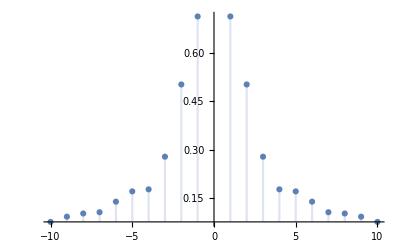

```mathematica
DiscretePlot[Abs[f],{w,-10,10},PlotRange->All]
```

```mathematica
(*6*)
```

```mathematica
Clear["`*"]
(*三角波*)
f[t_]:=TriangleWave[t];
a=FourierSeries[f[t],t,9]
```

1/(4 π)ⅇ^(-4 ⅈ t) (-ⅇ^-ⅈ+ⅇ^ⅈ+ⅇ^(-3 ⅈ)-ⅇ^(3 ⅈ)-ⅇ^(-5 ⅈ)+ⅇ^(5 ⅈ)+ⅇ^(-7 ⅈ)-ⅇ^(7 ⅈ)-ⅇ^(-9 ⅈ)+ⅇ^(9 ⅈ)+ⅇ^(-11 ⅈ)-ⅇ^(11 ⅈ)-4 ⅈ (-3+π))+1/(4 π)ⅇ^(4 ⅈ t) (ⅇ^-ⅈ-ⅇ^ⅈ-ⅇ^(-3 ⅈ)+ⅇ^(3 ⅈ)+ⅇ^(-5 ⅈ)-ⅇ^(5 ⅈ)-ⅇ^(-7 ⅈ)+ⅇ^(7 ⅈ)+ⅇ^(-9 ⅈ)-ⅇ^(9 ⅈ)-ⅇ^(-11 ⅈ)+ⅇ^(11 ⅈ)+4 ⅈ (-3+π))+1/(16 π)ⅇ^(-8 ⅈ t) (-ⅇ^(-2 ⅈ)+ⅇ^(2 ⅈ)+ⅇ^(-6 ⅈ)-ⅇ^(6 ⅈ)-ⅇ^(-10 ⅈ)+ⅇ^(10 ⅈ)+ⅇ^(-14 ⅈ)-ⅇ^(14 ⅈ)-ⅇ^(-18 ⅈ)+ⅇ^(18 ⅈ)+ⅇ^(-22 ⅈ)-ⅇ^(22 ⅈ)-8 ⅈ (-3+π))-1/π 4 ⅇ^(-(11 ⅈ)/4-ⅈ t) (-1+ⅇ^(ⅈ/2)-ⅇ^ⅈ+ⅇ^((3 ⅈ)/2)-ⅇ^(2 ⅈ)+ⅇ^((5 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((7 ⅈ)/2)-ⅇ^(4 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(5 ⅈ)+ⅇ^((11 ⅈ)/2)-ⅈ ⅇ^((11 ⅈ)/4) (-3+π))+1/π 4 ⅇ^(-(11 ⅈ)/4+ⅈ t) (-1+ⅇ^(ⅈ/2)-ⅇ^ⅈ+ⅇ^((3 ⅈ)/2)-ⅇ^(2 ⅈ)+ⅇ^((5 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((7 ⅈ)/2)-ⅇ^(4 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(5 ⅈ)+ⅇ^((11 ⅈ)/2)-ⅈ ⅇ^((11 ⅈ)/4) (-3+π))-1/π ⅇ^(-(11 ⅈ)/2-2 ⅈ t) (-1+ⅇ^ⅈ-ⅇ^(2 ⅈ)+ⅇ^(3 ⅈ)-ⅇ^(4 ⅈ)+ⅇ^(5 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(7 ⅈ)-ⅇ^(8 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(10 ⅈ)+ⅇ^(11 ⅈ)+2 ⅈ ⅇ^((11 ⅈ)/2) (-3+π))+1/π ⅇ^(-(11 ⅈ)/2+2 ⅈ t) (-1+ⅇ^ⅈ-ⅇ^(2 ⅈ)+ⅇ^(3 ⅈ)-ⅇ^(4 ⅈ)+ⅇ^(5 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(7 ⅈ)-ⅇ^(8 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(10 ⅈ)+ⅇ^(11 ⅈ)+2 ⅈ ⅇ^((11 ⅈ)/2) (-3+π))-1/(9 π)4 ⅇ^(-(33 ⅈ)/4-3 ⅈ t) (-1+ⅇ^((3 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(6 ⅈ)+ⅇ^((15 ⅈ)/2)-ⅇ^(9 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(12 ⅈ)+ⅇ^((27 ⅈ)/2)-ⅇ^(15 ⅈ)+ⅇ^((33 ⅈ)/2)-3 ⅈ ⅇ^((33 ⅈ)/4) (-3+π))+1/(9 π)4 ⅇ^(-(33 ⅈ)/4+3 ⅈ t) (-1+ⅇ^((3 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(6 ⅈ)+ⅇ^((15 ⅈ)/2)-ⅇ^(9 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(12 ⅈ)+ⅇ^((27 ⅈ)/2)-ⅇ^(15 ⅈ)+ⅇ^((33 ⅈ)/2)-3 ⅈ ⅇ^((33 ⅈ)/4) (-3+π))-1/(25 π)4 ⅇ^(-(55 ⅈ)/4-5 ⅈ t) (-1+ⅇ^((5 ⅈ)/2)-ⅇ^(5 ⅈ)+ⅇ^((15 ⅈ)/2)-ⅇ^(10 ⅈ)+ⅇ^((25 ⅈ)/2)-ⅇ^(15 ⅈ)+ⅇ^((35 ⅈ)/2)-ⅇ^(20 ⅈ)+ⅇ^((45 ⅈ)/2)-ⅇ^(25 ⅈ)+ⅇ^((55 ⅈ)/2)-5 ⅈ ⅇ^((55 ⅈ)/4) (-3+π))+1/(25 π)4 ⅇ^(-(55 ⅈ)/4+5 ⅈ t) (-1+ⅇ^((5 ⅈ)/2)-ⅇ^(5 ⅈ)+ⅇ^((15 ⅈ)/2)-ⅇ^(10 ⅈ)+ⅇ^((25 ⅈ)/2)-ⅇ^(15 ⅈ)+ⅇ^((35 ⅈ)/2)-ⅇ^(20 ⅈ)+ⅇ^((45 ⅈ)/2)-ⅇ^(25 ⅈ)+ⅇ^((55 ⅈ)/2)-5 ⅈ ⅇ^((55 ⅈ)/4) (-3+π))-1/(9 π)ⅇ^(-(33 ⅈ)/2-6 ⅈ t) (-1+ⅇ^(3 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(12 ⅈ)+ⅇ^(15 ⅈ)-ⅇ^(18 ⅈ)+ⅇ^(21 ⅈ)-ⅇ^(24 ⅈ)+ⅇ^(27 ⅈ)-ⅇ^(30 ⅈ)+ⅇ^(33 ⅈ)+6 ⅈ ⅇ^((33 ⅈ)/2) (-3+π))+1/(9 π)ⅇ^(-(33 ⅈ)/2+6 ⅈ t) (-1+ⅇ^(3 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(12 ⅈ)+ⅇ^(15 ⅈ)-ⅇ^(18 ⅈ)+ⅇ^(21 ⅈ)-ⅇ^(24 ⅈ)+ⅇ^(27 ⅈ)-ⅇ^(30 ⅈ)+ⅇ^(33 ⅈ)+6 ⅈ ⅇ^((33 ⅈ)/2) (-3+π))-1/(49 π)4 ⅇ^(-(77 ⅈ)/4-7 ⅈ t) (-1+ⅇ^((7 ⅈ)/2)-ⅇ^(7 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(14 ⅈ)+ⅇ^((35 ⅈ)/2)-ⅇ^(21 ⅈ)+ⅇ^((49 ⅈ)/2)-ⅇ^(28 ⅈ)+ⅇ^((63 ⅈ)/2)-ⅇ^(35 ⅈ)+ⅇ^((77 ⅈ)/2)-7 ⅈ ⅇ^((77 ⅈ)/4) (-3+π))+1/(49 π)4 ⅇ^(-(77 ⅈ)/4+7 ⅈ t) (-1+ⅇ^((7 ⅈ)/2)-ⅇ^(7 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(14 ⅈ)+ⅇ^((35 ⅈ)/2)-ⅇ^(21 ⅈ)+ⅇ^((49 ⅈ)/2)-ⅇ^(28 ⅈ)+ⅇ^((63 ⅈ)/2)-ⅇ^(35 ⅈ)+ⅇ^((77 ⅈ)/2)-7 ⅈ ⅇ^((77 ⅈ)/4) (-3+π))+1/(16 π)ⅇ^(-22 ⅈ+8 ⅈ t) (-1+ⅇ^(4 ⅈ)-ⅇ^(8 ⅈ)+ⅇ^(12 ⅈ)-ⅇ^(16 ⅈ)+ⅇ^(20 ⅈ)-ⅇ^(24 ⅈ)+ⅇ^(28 ⅈ)-ⅇ^(32 ⅈ)+ⅇ^(36 ⅈ)-ⅇ^(40 ⅈ)+ⅇ^(44 ⅈ)+8 ⅈ ⅇ^(22 ⅈ) (-3+π))-1/(81 π)4 ⅇ^(-(99 ⅈ)/4-9 ⅈ t) (-1+ⅇ^((9 ⅈ)/2)-ⅇ^(9 ⅈ)+ⅇ^((27 ⅈ)/2)-ⅇ^(18 ⅈ)+ⅇ^((45 ⅈ)/2)-ⅇ^(27 ⅈ)+ⅇ^((63 ⅈ)/2)-ⅇ^(36 ⅈ)+ⅇ^((81 ⅈ)/2)-ⅇ^(45 ⅈ)+ⅇ^((99 ⅈ)/2)-9 ⅈ ⅇ^((99 ⅈ)/4) (-3+π))+1/(81 π)4 ⅇ^(-(99 ⅈ)/4+9 ⅈ t) (-1+ⅇ^((9 ⅈ)/2)-ⅇ^(9 ⅈ)+ⅇ^((27 ⅈ)/2)-ⅇ^(18 ⅈ)+ⅇ^((45 ⅈ)/2)-ⅇ^(27 ⅈ)+ⅇ^((63 ⅈ)/2)-ⅇ^(36 ⅈ)+ⅇ^((81 ⅈ)/2)-ⅇ^(45 ⅈ)+ⅇ^((99 ⅈ)/2)-9 ⅈ ⅇ^((99 ⅈ)/4) (-3+π))

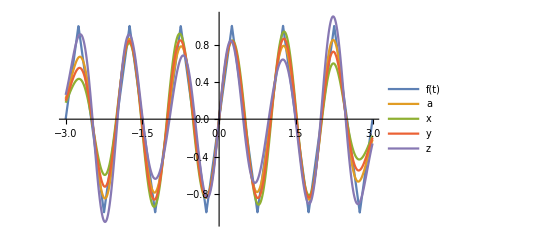

```mathematica
x=1/(16 π)ⅇ^(-8 ⅈ t) (-ⅇ^(-2 ⅈ)+ⅇ^(2 ⅈ)+ⅇ^(-6 ⅈ)-ⅇ^(6 ⅈ)-ⅇ^(-10 ⅈ)+ⅇ^(10 ⅈ)+ⅇ^(-14 ⅈ)-ⅇ^(14 ⅈ)-ⅇ^(-18 ⅈ)+ⅇ^(18 ⅈ)+ⅇ^(-22 ⅈ)-ⅇ^(22 ⅈ)-8 ⅈ (-3+π))-1/π 4 ⅇ^(-(11 ⅈ)/4-ⅈ t) (-1+ⅇ^(ⅈ/2)-ⅇ^ⅈ+ⅇ^((3 ⅈ)/2)-ⅇ^(2 ⅈ)+ⅇ^((5 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((7 ⅈ)/2)-ⅇ^(4 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(5 ⅈ)+ⅇ^((11 ⅈ)/2)-ⅈ ⅇ^((11 ⅈ)/4) (-3+π))+1/π 4 ⅇ^(-(11 ⅈ)/4+ⅈ t) (-1+ⅇ^(ⅈ/2)-ⅇ^ⅈ+ⅇ^((3 ⅈ)/2)-ⅇ^(2 ⅈ)+ⅇ^((5 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((7 ⅈ)/2)-ⅇ^(4 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(5 ⅈ)+ⅇ^((11 ⅈ)/2)-ⅈ ⅇ^((11 ⅈ)/4) (-3+π))-1/π ⅇ^(-(11 ⅈ)/2-2 ⅈ t) (-1+ⅇ^ⅈ-ⅇ^(2 ⅈ)+ⅇ^(3 ⅈ)-ⅇ^(4 ⅈ)+ⅇ^(5 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(7 ⅈ)-ⅇ^(8 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(10 ⅈ)+ⅇ^(11 ⅈ)+2 ⅈ ⅇ^((11 ⅈ)/2) (-3+π))+1/π ⅇ^(-(11 ⅈ)/2+2 ⅈ t) (-1+ⅇ^ⅈ-ⅇ^(2 ⅈ)+ⅇ^(3 ⅈ)-ⅇ^(4 ⅈ)+ⅇ^(5 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(7 ⅈ)-ⅇ^(8 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(10 ⅈ)+ⅇ^(11 ⅈ)+2 ⅈ ⅇ^((11 ⅈ)/2) (-3+π))-1/(9 π)4 ⅇ^(-(33 ⅈ)/4-3 ⅈ t) (-1+ⅇ^((3 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(6 ⅈ)+ⅇ^((15 ⅈ)/2)-ⅇ^(9 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(12 ⅈ)+ⅇ^((27 ⅈ)/2)-ⅇ^(15 ⅈ)+ⅇ^((33 ⅈ)/2)-3 ⅈ ⅇ^((33 ⅈ)/4) (-3+π))+1/(9 π)4 ⅇ^(-(33 ⅈ)/4+3 ⅈ t) (-1+ⅇ^((3 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(6 ⅈ)+ⅇ^((15 ⅈ)/2)-ⅇ^(9 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(12 ⅈ)+ⅇ^((27 ⅈ)/2)-ⅇ^(15 ⅈ)+ⅇ^((33 ⅈ)/2)-3 ⅈ ⅇ^((33 ⅈ)/4) (-3+π))-1/(9 π)ⅇ^(-(33 ⅈ)/2-6 ⅈ t) (-1+ⅇ^(3 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(12 ⅈ)+ⅇ^(15 ⅈ)-ⅇ^(18 ⅈ)+ⅇ^(21 ⅈ)-ⅇ^(24 ⅈ)+ⅇ^(27 ⅈ)-ⅇ^(30 ⅈ)+ⅇ^(33 ⅈ)+6 ⅈ ⅇ^((33 ⅈ)/2) (-3+π))+1/(9 π)ⅇ^(-(33 ⅈ)/2+6 ⅈ t) (-1+ⅇ^(3 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(12 ⅈ)+ⅇ^(15 ⅈ)-ⅇ^(18 ⅈ)+ⅇ^(21 ⅈ)-ⅇ^(24 ⅈ)+ⅇ^(27 ⅈ)-ⅇ^(30 ⅈ)+ⅇ^(33 ⅈ)+6 ⅈ ⅇ^((33 ⅈ)/2) (-3+π))-1/(49 π)4 ⅇ^(-(77 ⅈ)/4-7 ⅈ t) (-1+ⅇ^((7 ⅈ)/2)-ⅇ^(7 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(14 ⅈ)+ⅇ^((35 ⅈ)/2)-ⅇ^(21 ⅈ)+ⅇ^((49 ⅈ)/2)-ⅇ^(28 ⅈ)+ⅇ^((63 ⅈ)/2)-ⅇ^(35 ⅈ)+ⅇ^((77 ⅈ)/2)-7 ⅈ ⅇ^((77 ⅈ)/4) (-3+π))+1/(49 π)4 ⅇ^(-(77 ⅈ)/4+7 ⅈ t) (-1+ⅇ^((7 ⅈ)/2)-ⅇ^(7 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(14 ⅈ)+ⅇ^((35 ⅈ)/2)-ⅇ^(21 ⅈ)+ⅇ^((49 ⅈ)/2)-ⅇ^(28 ⅈ)+ⅇ^((63 ⅈ)/2)-ⅇ^(35 ⅈ)+ⅇ^((77 ⅈ)/2)-7 ⅈ ⅇ^((77 ⅈ)/4) (-3+π))+1/(16 π)ⅇ^(-22 ⅈ+8 ⅈ t) (-1+ⅇ^(4 ⅈ)-ⅇ^(8 ⅈ)+ⅇ^(12 ⅈ)-ⅇ^(16 ⅈ)+ⅇ^(20 ⅈ)-ⅇ^(24 ⅈ)+ⅇ^(28 ⅈ)-ⅇ^(32 ⅈ)+ⅇ^(36 ⅈ)-ⅇ^(40 ⅈ)+ⅇ^(44 ⅈ)+8 ⅈ ⅇ^(22 ⅈ) (-3+π));
y=1/(2*4 π)ⅇ^(-4 ⅈ t) (-ⅇ^-ⅈ+ⅇ^ⅈ+ⅇ^(-3 ⅈ)-ⅇ^(3 ⅈ)-ⅇ^(-5 ⅈ)+ⅇ^(5 ⅈ)+ⅇ^(-7 ⅈ)-ⅇ^(7 ⅈ)-ⅇ^(-9 ⅈ)+ⅇ^(9 ⅈ)+ⅇ^(-11 ⅈ)-ⅇ^(11 ⅈ)-4 ⅈ (-3+π))+1/(2*4 π)ⅇ^(4 ⅈ t) (ⅇ^-ⅈ-ⅇ^ⅈ-ⅇ^(-3 ⅈ)+ⅇ^(3 ⅈ)+ⅇ^(-5 ⅈ)-ⅇ^(5 ⅈ)-ⅇ^(-7 ⅈ)+ⅇ^(7 ⅈ)+ⅇ^(-9 ⅈ)-ⅇ^(9 ⅈ)-ⅇ^(-11 ⅈ)+ⅇ^(11 ⅈ)+4 ⅈ (-3+π))+1/(16 π)ⅇ^(-8 ⅈ t) (-ⅇ^(-2 ⅈ)+ⅇ^(2 ⅈ)+ⅇ^(-6 ⅈ)-ⅇ^(6 ⅈ)-ⅇ^(-10 ⅈ)+ⅇ^(10 ⅈ)+ⅇ^(-14 ⅈ)-ⅇ^(14 ⅈ)-ⅇ^(-18 ⅈ)+ⅇ^(18 ⅈ)+ⅇ^(-22 ⅈ)-ⅇ^(22 ⅈ)-8 ⅈ (-3+π))-1/π 4 ⅇ^(-(11 ⅈ)/4-ⅈ t) (-1+ⅇ^(ⅈ/2)-ⅇ^ⅈ+ⅇ^((3 ⅈ)/2)-ⅇ^(2 ⅈ)+ⅇ^((5 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((7 ⅈ)/2)-ⅇ^(4 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(5 ⅈ)+ⅇ^((11 ⅈ)/2)-ⅈ ⅇ^((11 ⅈ)/4) (-3+π))+1/π 4 ⅇ^(-(11 ⅈ)/4+ⅈ t) (-1+ⅇ^(ⅈ/2)-ⅇ^ⅈ+ⅇ^((3 ⅈ)/2)-ⅇ^(2 ⅈ)+ⅇ^((5 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((7 ⅈ)/2)-ⅇ^(4 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(5 ⅈ)+ⅇ^((11 ⅈ)/2)-ⅈ ⅇ^((11 ⅈ)/4) (-3+π))-1/π ⅇ^(-(11 ⅈ)/2-2 ⅈ t) (-1+ⅇ^ⅈ-ⅇ^(2 ⅈ)+ⅇ^(3 ⅈ)-ⅇ^(4 ⅈ)+ⅇ^(5 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(7 ⅈ)-ⅇ^(8 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(10 ⅈ)+ⅇ^(11 ⅈ)+2 ⅈ ⅇ^((11 ⅈ)/2) (-3+π))+1/π ⅇ^(-(11 ⅈ)/2+2 ⅈ t) (-1+ⅇ^ⅈ-ⅇ^(2 ⅈ)+ⅇ^(3 ⅈ)-ⅇ^(4 ⅈ)+ⅇ^(5 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(7 ⅈ)-ⅇ^(8 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(10 ⅈ)+ⅇ^(11 ⅈ)+2 ⅈ ⅇ^((11 ⅈ)/2) (-3+π))-1/(9 π)4 ⅇ^(-(33 ⅈ)/4-3 ⅈ t) (-1+ⅇ^((3 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(6 ⅈ)+ⅇ^((15 ⅈ)/2)-ⅇ^(9 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(12 ⅈ)+ⅇ^((27 ⅈ)/2)-ⅇ^(15 ⅈ)+ⅇ^((33 ⅈ)/2)-3 ⅈ ⅇ^((33 ⅈ)/4) (-3+π))+1/(9 π)4 ⅇ^(-(33 ⅈ)/4+3 ⅈ t) (-1+ⅇ^((3 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(6 ⅈ)+ⅇ^((15 ⅈ)/2)-ⅇ^(9 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(12 ⅈ)+ⅇ^((27 ⅈ)/2)-ⅇ^(15 ⅈ)+ⅇ^((33 ⅈ)/2)-3 ⅈ ⅇ^((33 ⅈ)/4) (-3+π))-1/(2*25 π)4 ⅇ^(-(55 ⅈ)/4-5 ⅈ t) (-1+ⅇ^((5 ⅈ)/2)-ⅇ^(5 ⅈ)+ⅇ^((15 ⅈ)/2)-ⅇ^(10 ⅈ)+ⅇ^((25 ⅈ)/2)-ⅇ^(15 ⅈ)+ⅇ^((35 ⅈ)/2)-ⅇ^(20 ⅈ)+ⅇ^((45 ⅈ)/2)-ⅇ^(25 ⅈ)+ⅇ^((55 ⅈ)/2)-5 ⅈ ⅇ^((55 ⅈ)/4) (-3+π))+1/(2*25 π)4 ⅇ^(-(55 ⅈ)/4+5 ⅈ t) (-1+ⅇ^((5 ⅈ)/2)-ⅇ^(5 ⅈ)+ⅇ^((15 ⅈ)/2)-ⅇ^(10 ⅈ)+ⅇ^((25 ⅈ)/2)-ⅇ^(15 ⅈ)+ⅇ^((35 ⅈ)/2)-ⅇ^(20 ⅈ)+ⅇ^((45 ⅈ)/2)-ⅇ^(25 ⅈ)+ⅇ^((55 ⅈ)/2)-5 ⅈ ⅇ^((55 ⅈ)/4) (-3+π))-1/(9 π)ⅇ^(-(33 ⅈ)/2-6 ⅈ t) (-1+ⅇ^(3 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(12 ⅈ)+ⅇ^(15 ⅈ)-ⅇ^(18 ⅈ)+ⅇ^(21 ⅈ)-ⅇ^(24 ⅈ)+ⅇ^(27 ⅈ)-ⅇ^(30 ⅈ)+ⅇ^(33 ⅈ)+6 ⅈ ⅇ^((33 ⅈ)/2) (-3+π))+1/(9 π)ⅇ^(-(33 ⅈ)/2+6 ⅈ t) (-1+ⅇ^(3 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(12 ⅈ)+ⅇ^(15 ⅈ)-ⅇ^(18 ⅈ)+ⅇ^(21 ⅈ)-ⅇ^(24 ⅈ)+ⅇ^(27 ⅈ)-ⅇ^(30 ⅈ)+ⅇ^(33 ⅈ)+6 ⅈ ⅇ^((33 ⅈ)/2) (-3+π))-1/(49 π)4 ⅇ^(-(77 ⅈ)/4-7 ⅈ t) (-1+ⅇ^((7 ⅈ)/2)-ⅇ^(7 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(14 ⅈ)+ⅇ^((35 ⅈ)/2)-ⅇ^(21 ⅈ)+ⅇ^((49 ⅈ)/2)-ⅇ^(28 ⅈ)+ⅇ^((63 ⅈ)/2)-ⅇ^(35 ⅈ)+ⅇ^((77 ⅈ)/2)-7 ⅈ ⅇ^((77 ⅈ)/4) (-3+π))+1/(49 π)4 ⅇ^(-(77 ⅈ)/4+7 ⅈ t) (-1+ⅇ^((7 ⅈ)/2)-ⅇ^(7 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(14 ⅈ)+ⅇ^((35 ⅈ)/2)-ⅇ^(21 ⅈ)+ⅇ^((49 ⅈ)/2)-ⅇ^(28 ⅈ)+ⅇ^((63 ⅈ)/2)-ⅇ^(35 ⅈ)+ⅇ^((77 ⅈ)/2)-7 ⅈ ⅇ^((77 ⅈ)/4) (-3+π))+1/(16 π)ⅇ^(-22 ⅈ+8 ⅈ t) (-1+ⅇ^(4 ⅈ)-ⅇ^(8 ⅈ)+ⅇ^(12 ⅈ)-ⅇ^(16 ⅈ)+ⅇ^(20 ⅈ)-ⅇ^(24 ⅈ)+ⅇ^(28 ⅈ)-ⅇ^(32 ⅈ)+ⅇ^(36 ⅈ)-ⅇ^(40 ⅈ)+ⅇ^(44 ⅈ)+8 ⅈ ⅇ^(22 ⅈ) (-3+π))-1/(2*81 π)4 ⅇ^(-(99 ⅈ)/4-9 ⅈ t) (-1+ⅇ^((9 ⅈ)/2)-ⅇ^(9 ⅈ)+ⅇ^((27 ⅈ)/2)-ⅇ^(18 ⅈ)+ⅇ^((45 ⅈ)/2)-ⅇ^(27 ⅈ)+ⅇ^((63 ⅈ)/2)-ⅇ^(36 ⅈ)+ⅇ^((81 ⅈ)/2)-ⅇ^(45 ⅈ)+ⅇ^((99 ⅈ)/2)-9 ⅈ ⅇ^((99 ⅈ)/4) (-3+π))+1/(2*81 π)4 ⅇ^(-(99 ⅈ)/4+9 ⅈ t) (-1+ⅇ^((9 ⅈ)/2)-ⅇ^(9 ⅈ)+ⅇ^((27 ⅈ)/2)-ⅇ^(18 ⅈ)+ⅇ^((45 ⅈ)/2)-ⅇ^(27 ⅈ)+ⅇ^((63 ⅈ)/2)-ⅇ^(36 ⅈ)+ⅇ^((81 ⅈ)/2)-ⅇ^(45 ⅈ)+ⅇ^((99 ⅈ)/2)-9 ⅈ ⅇ^((99 ⅈ)/4) (-3+π));
z=2/(4 π)ⅇ^(-4 ⅈ t) (-ⅇ^-ⅈ+ⅇ^ⅈ+ⅇ^(-3 ⅈ)-ⅇ^(3 ⅈ)-ⅇ^(-5 ⅈ)+ⅇ^(5 ⅈ)+ⅇ^(-7 ⅈ)-ⅇ^(7 ⅈ)-ⅇ^(-9 ⅈ)+ⅇ^(9 ⅈ)+ⅇ^(-11 ⅈ)-ⅇ^(11 ⅈ)-4 ⅈ (-3+π))+2/(4 π)ⅇ^(4 ⅈ t) (ⅇ^-ⅈ-ⅇ^ⅈ-ⅇ^(-3 ⅈ)+ⅇ^(3 ⅈ)+ⅇ^(-5 ⅈ)-ⅇ^(5 ⅈ)-ⅇ^(-7 ⅈ)+ⅇ^(7 ⅈ)+ⅇ^(-9 ⅈ)-ⅇ^(9 ⅈ)-ⅇ^(-11 ⅈ)+ⅇ^(11 ⅈ)+4 ⅈ (-3+π))+1/(16 π)ⅇ^(-8 ⅈ t) (-ⅇ^(-2 ⅈ)+ⅇ^(2 ⅈ)+ⅇ^(-6 ⅈ)-ⅇ^(6 ⅈ)-ⅇ^(-10 ⅈ)+ⅇ^(10 ⅈ)+ⅇ^(-14 ⅈ)-ⅇ^(14 ⅈ)-ⅇ^(-18 ⅈ)+ⅇ^(18 ⅈ)+ⅇ^(-22 ⅈ)-ⅇ^(22 ⅈ)-8 ⅈ (-3+π))-1/π 4 ⅇ^(-(11 ⅈ)/4-ⅈ t) (-1+ⅇ^(ⅈ/2)-ⅇ^ⅈ+ⅇ^((3 ⅈ)/2)-ⅇ^(2 ⅈ)+ⅇ^((5 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((7 ⅈ)/2)-ⅇ^(4 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(5 ⅈ)+ⅇ^((11 ⅈ)/2)-ⅈ ⅇ^((11 ⅈ)/4) (-3+π))+1/π 4 ⅇ^(-(11 ⅈ)/4+ⅈ t) (-1+ⅇ^(ⅈ/2)-ⅇ^ⅈ+ⅇ^((3 ⅈ)/2)-ⅇ^(2 ⅈ)+ⅇ^((5 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((7 ⅈ)/2)-ⅇ^(4 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(5 ⅈ)+ⅇ^((11 ⅈ)/2)-ⅈ ⅇ^((11 ⅈ)/4) (-3+π))-1/π ⅇ^(-(11 ⅈ)/2-2 ⅈ t) (-1+ⅇ^ⅈ-ⅇ^(2 ⅈ)+ⅇ^(3 ⅈ)-ⅇ^(4 ⅈ)+ⅇ^(5 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(7 ⅈ)-ⅇ^(8 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(10 ⅈ)+ⅇ^(11 ⅈ)+2 ⅈ ⅇ^((11 ⅈ)/2) (-3+π))+1/π ⅇ^(-(11 ⅈ)/2+2 ⅈ t) (-1+ⅇ^ⅈ-ⅇ^(2 ⅈ)+ⅇ^(3 ⅈ)-ⅇ^(4 ⅈ)+ⅇ^(5 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(7 ⅈ)-ⅇ^(8 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(10 ⅈ)+ⅇ^(11 ⅈ)+2 ⅈ ⅇ^((11 ⅈ)/2) (-3+π))-1/(9 π)4 ⅇ^(-(33 ⅈ)/4-3 ⅈ t) (-1+ⅇ^((3 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(6 ⅈ)+ⅇ^((15 ⅈ)/2)-ⅇ^(9 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(12 ⅈ)+ⅇ^((27 ⅈ)/2)-ⅇ^(15 ⅈ)+ⅇ^((33 ⅈ)/2)-3 ⅈ ⅇ^((33 ⅈ)/4) (-3+π))+1/(9 π)4 ⅇ^(-(33 ⅈ)/4+3 ⅈ t) (-1+ⅇ^((3 ⅈ)/2)-ⅇ^(3 ⅈ)+ⅇ^((9 ⅈ)/2)-ⅇ^(6 ⅈ)+ⅇ^((15 ⅈ)/2)-ⅇ^(9 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(12 ⅈ)+ⅇ^((27 ⅈ)/2)-ⅇ^(15 ⅈ)+ⅇ^((33 ⅈ)/2)-3 ⅈ ⅇ^((33 ⅈ)/4) (-3+π))-2/(25 π)4 ⅇ^(-(55 ⅈ)/4-5 ⅈ t) (-1+ⅇ^((5 ⅈ)/2)-ⅇ^(5 ⅈ)+ⅇ^((15 ⅈ)/2)-ⅇ^(10 ⅈ)+ⅇ^((25 ⅈ)/2)-ⅇ^(15 ⅈ)+ⅇ^((35 ⅈ)/2)-ⅇ^(20 ⅈ)+ⅇ^((45 ⅈ)/2)-ⅇ^(25 ⅈ)+ⅇ^((55 ⅈ)/2)-5 ⅈ ⅇ^((55 ⅈ)/4) (-3+π))+2/(25 π)4 ⅇ^(-(55 ⅈ)/4+5 ⅈ t) (-1+ⅇ^((5 ⅈ)/2)-ⅇ^(5 ⅈ)+ⅇ^((15 ⅈ)/2)-ⅇ^(10 ⅈ)+ⅇ^((25 ⅈ)/2)-ⅇ^(15 ⅈ)+ⅇ^((35 ⅈ)/2)-ⅇ^(20 ⅈ)+ⅇ^((45 ⅈ)/2)-ⅇ^(25 ⅈ)+ⅇ^((55 ⅈ)/2)-5 ⅈ ⅇ^((55 ⅈ)/4) (-3+π))-1/(9 π)ⅇ^(-(33 ⅈ)/2-6 ⅈ t) (-1+ⅇ^(3 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(12 ⅈ)+ⅇ^(15 ⅈ)-ⅇ^(18 ⅈ)+ⅇ^(21 ⅈ)-ⅇ^(24 ⅈ)+ⅇ^(27 ⅈ)-ⅇ^(30 ⅈ)+ⅇ^(33 ⅈ)+6 ⅈ ⅇ^((33 ⅈ)/2) (-3+π))+1/(9 π)ⅇ^(-(33 ⅈ)/2+6 ⅈ t) (-1+ⅇ^(3 ⅈ)-ⅇ^(6 ⅈ)+ⅇ^(9 ⅈ)-ⅇ^(12 ⅈ)+ⅇ^(15 ⅈ)-ⅇ^(18 ⅈ)+ⅇ^(21 ⅈ)-ⅇ^(24 ⅈ)+ⅇ^(27 ⅈ)-ⅇ^(30 ⅈ)+ⅇ^(33 ⅈ)+6 ⅈ ⅇ^((33 ⅈ)/2) (-3+π))-1/(49 π)4 ⅇ^(-(77 ⅈ)/4-7 ⅈ t) (-1+ⅇ^((7 ⅈ)/2)-ⅇ^(7 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(14 ⅈ)+ⅇ^((35 ⅈ)/2)-ⅇ^(21 ⅈ)+ⅇ^((49 ⅈ)/2)-ⅇ^(28 ⅈ)+ⅇ^((63 ⅈ)/2)-ⅇ^(35 ⅈ)+ⅇ^((77 ⅈ)/2)-7 ⅈ ⅇ^((77 ⅈ)/4) (-3+π))+1/(49 π)4 ⅇ^(-(77 ⅈ)/4+7 ⅈ t) (-1+ⅇ^((7 ⅈ)/2)-ⅇ^(7 ⅈ)+ⅇ^((21 ⅈ)/2)-ⅇ^(14 ⅈ)+ⅇ^((35 ⅈ)/2)-ⅇ^(21 ⅈ)+ⅇ^((49 ⅈ)/2)-ⅇ^(28 ⅈ)+ⅇ^((63 ⅈ)/2)-ⅇ^(35 ⅈ)+ⅇ^((77 ⅈ)/2)-7 ⅈ ⅇ^((77 ⅈ)/4) (-3+π))+1/(16 π)ⅇ^(-22 ⅈ+8 ⅈ t) (-1+ⅇ^(4 ⅈ)-ⅇ^(8 ⅈ)+ⅇ^(12 ⅈ)-ⅇ^(16 ⅈ)+ⅇ^(20 ⅈ)-ⅇ^(24 ⅈ)+ⅇ^(28 ⅈ)-ⅇ^(32 ⅈ)+ⅇ^(36 ⅈ)-ⅇ^(40 ⅈ)+ⅇ^(44 ⅈ)+8 ⅈ ⅇ^(22 ⅈ) (-3+π))-2/(81 π)4 ⅇ^(-(99 ⅈ)/4-9 ⅈ t) (-1+ⅇ^((9 ⅈ)/2)-ⅇ^(9 ⅈ)+ⅇ^((27 ⅈ)/2)-ⅇ^(18 ⅈ)+ⅇ^((45 ⅈ)/2)-ⅇ^(27 ⅈ)+ⅇ^((63 ⅈ)/2)-ⅇ^(36 ⅈ)+ⅇ^((81 ⅈ)/2)-ⅇ^(45 ⅈ)+ⅇ^((99 ⅈ)/2)-9 ⅈ ⅇ^((99 ⅈ)/4) (-3+π))+2/(81 π)4 ⅇ^(-(99 ⅈ)/4+9 ⅈ t) (-1+ⅇ^((9 ⅈ)/2)-ⅇ^(9 ⅈ)+ⅇ^((27 ⅈ)/2)-ⅇ^(18 ⅈ)+ⅇ^((45 ⅈ)/2)-ⅇ^(27 ⅈ)+ⅇ^((63 ⅈ)/2)-ⅇ^(36 ⅈ)+ⅇ^((81 ⅈ)/2)-ⅇ^(45 ⅈ)+ⅇ^((99 ⅈ)/2)-9 ⅈ ⅇ^((99 ⅈ)/4) (-3+π));
Plot[{f[t],a,x,y,z},{t,-3,3},PlotLegends->"Expressions"]
```

```mathematica
Clear["`*"]
f[t_]:=Which[-1<=t<=0,-1,0<=t<=1,1]
f[t_]:=f[t-2 ]/;t≥1
f[t_]:=f[t+2]/;t≤-1
w=FourierSeries[f[t],t,9]
```

(ⅈ (-1+ⅇ^ⅈ)^2 ⅇ^(-ⅈ+ⅈ t))/(2 π)+(ⅈ (-1+ⅇ^(2 ⅈ))^2 ⅇ^(-2 ⅈ+2 ⅈ t))/(4 π)-(ⅈ (-1+ⅇ^(3 ⅈ))^2 ⅇ^(-3 ⅈ-3 ⅈ t))/(6 π)+(ⅈ (-1+ⅇ^(3 ⅈ))^2 ⅇ^(-3 ⅈ+3 ⅈ t))/(6 π)-(ⅈ (-1+ⅇ^(4 ⅈ))^2 ⅇ^(-4 ⅈ-4 ⅈ t))/(8 π)+(ⅈ (-1+ⅇ^(4 ⅈ))^2 ⅇ^(-4 ⅈ+4 ⅈ t))/(8 π)-(ⅈ (-1+ⅇ^(5 ⅈ))^2 ⅇ^(-5 ⅈ-5 ⅈ t))/(10 π)+(ⅈ (-1+ⅇ^(5 ⅈ))^2 ⅇ^(-5 ⅈ+5 ⅈ t))/(10 π)-(ⅈ (-1+ⅇ^(6 ⅈ))^2 ⅇ^(-6 ⅈ-6 ⅈ t))/(12 π)+(ⅈ (-1+ⅇ^(6 ⅈ))^2 ⅇ^(-6 ⅈ+6 ⅈ t))/(12 π)-(ⅈ (-1+ⅇ^(7 ⅈ))^2 ⅇ^(-7 ⅈ-7 ⅈ t))/(14 π)+(ⅈ (-1+ⅇ^(7 ⅈ))^2 ⅇ^(-7 ⅈ+7 ⅈ t))/(14 π)-(ⅈ (-1+ⅇ^(8 ⅈ))^2 ⅇ^(-8 ⅈ-8 ⅈ t))/(16 π)+(ⅈ (-1+ⅇ^(8 ⅈ))^2 ⅇ^(-8 ⅈ+8 ⅈ t))/(16 π)-(ⅈ (-1+ⅇ^(9 ⅈ))^2 ⅇ^(-9 ⅈ-9 ⅈ t))/(18 π)+(ⅈ (-1+ⅇ^(9 ⅈ))^2 ⅇ^(-9 ⅈ+9 ⅈ t))/(18 π)+(2 ⅈ ⅇ^(-ⅈ t) Sin[1/2]^2)/π+((-1+ⅇ^(2 ⅈ)) ⅇ^(-ⅈ-2 ⅈ t) Sin[1])/(2 π)

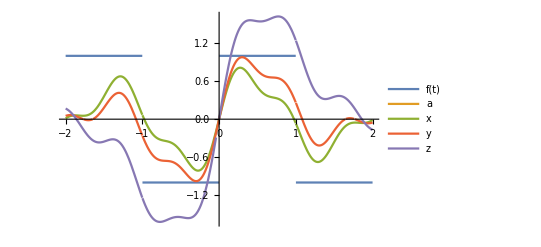

```mathematica
x=-(ⅈ (-1+ⅇ^(3 ⅈ))^2 ⅇ^(-3 ⅈ-3 ⅈ t))/(6 π)+(ⅈ (-1+ⅇ^(3 ⅈ))^2 ⅇ^(-3 ⅈ+3 ⅈ t))/(6 π)-(ⅈ (-1+ⅇ^(4 ⅈ))^2 ⅇ^(-4 ⅈ-4 ⅈ t))/(8 π)+(ⅈ (-1+ⅇ^(4 ⅈ))^2 ⅇ^(-4 ⅈ+4 ⅈ t))/(8 π)-(ⅈ (-1+ⅇ^(5 ⅈ))^2 ⅇ^(-5 ⅈ-5 ⅈ t))/(10 π)+(ⅈ (-1+ⅇ^(5 ⅈ))^2 ⅇ^(-5 ⅈ+5 ⅈ t))/(10 π)-(ⅈ (-1+ⅇ^(7 ⅈ))^2 ⅇ^(-7 ⅈ-7 ⅈ t))/(14 π)+(ⅈ (-1+ⅇ^(7 ⅈ))^2 ⅇ^(-7 ⅈ+7 ⅈ t))/(14 π)-(ⅈ (-1+ⅇ^(8 ⅈ))^2 ⅇ^(-8 ⅈ-8 ⅈ t))/(16 π)+(ⅈ (-1+ⅇ^(8 ⅈ))^2 ⅇ^(-8 ⅈ+8 ⅈ t))/(16 π)-(ⅈ (-1+ⅇ^(9 ⅈ))^2 ⅇ^(-9 ⅈ-9 ⅈ t))/(18 π)+(ⅈ (-1+ⅇ^(9 ⅈ))^2 ⅇ^(-9 ⅈ+9 ⅈ t))/(18 π);
y=(ⅈ (-1+ⅇ^ⅈ)^2 ⅇ^(-ⅈ+ⅈ t))/(2*2 π)+(ⅈ (-1+ⅇ^(2 ⅈ))^2 ⅇ^(-2 ⅈ+2 ⅈ t))/(2*4 π)-(ⅈ (-1+ⅇ^(3 ⅈ))^2 ⅇ^(-3 ⅈ-3 ⅈ t))/(6 π)+(ⅈ (-1+ⅇ^(3 ⅈ))^2 ⅇ^(-3 ⅈ+3 ⅈ t))/(6 π)-(ⅈ (-1+ⅇ^(4 ⅈ))^2 ⅇ^(-4 ⅈ-4 ⅈ t))/(8 π)+(ⅈ (-1+ⅇ^(4 ⅈ))^2 ⅇ^(-4 ⅈ+4 ⅈ t))/(8 π)-(ⅈ (-1+ⅇ^(5 ⅈ))^2 ⅇ^(-5 ⅈ-5 ⅈ t))/(10 π)+(ⅈ (-1+ⅇ^(5 ⅈ))^2 ⅇ^(-5 ⅈ+5 ⅈ t))/(10 π)-(ⅈ (-1+ⅇ^(6 ⅈ))^2 ⅇ^(-6 ⅈ-6 ⅈ t))/(2*12 π)+(ⅈ (-1+ⅇ^(6 ⅈ))^2 ⅇ^(-6 ⅈ+6 ⅈ t))/(2*12 π)-(ⅈ (-1+ⅇ^(7 ⅈ))^2 ⅇ^(-7 ⅈ-7 ⅈ t))/(14 π)+(ⅈ (-1+ⅇ^(7 ⅈ))^2 ⅇ^(-7 ⅈ+7 ⅈ t))/(14 π)-(ⅈ (-1+ⅇ^(8 ⅈ))^2 ⅇ^(-8 ⅈ-8 ⅈ t))/(16 π)+(ⅈ (-1+ⅇ^(8 ⅈ))^2 ⅇ^(-8 ⅈ+8 ⅈ t))/(16 π)-(ⅈ (-1+ⅇ^(9 ⅈ))^2 ⅇ^(-9 ⅈ-9 ⅈ t))/(18 π)+(ⅈ (-1+ⅇ^(9 ⅈ))^2 ⅇ^(-9 ⅈ+9 ⅈ t))/(18 π)+(2 ⅈ ⅇ^(-ⅈ t) Sin[1/2]^2)/(2*π)+((-1+ⅇ^(2 ⅈ)) ⅇ^(-ⅈ-2 ⅈ t) Sin[1])/(2*2 π);
z=(2*ⅈ (-1+ⅇ^ⅈ)^2 ⅇ^(-ⅈ+ⅈ t))/(2 π)+(2*ⅈ (-1+ⅇ^(2 ⅈ))^2 ⅇ^(-2 ⅈ+2 ⅈ t))/(4 π)-(ⅈ (-1+ⅇ^(3 ⅈ))^2 ⅇ^(-3 ⅈ-3 ⅈ t))/(6 π)+(ⅈ (-1+ⅇ^(3 ⅈ))^2 ⅇ^(-3 ⅈ+3 ⅈ t))/(6 π)-(ⅈ (-1+ⅇ^(4 ⅈ))^2 ⅇ^(-4 ⅈ-4 ⅈ t))/(8 π)+(ⅈ (-1+ⅇ^(4 ⅈ))^2 ⅇ^(-4 ⅈ+4 ⅈ t))/(8 π)-(ⅈ (-1+ⅇ^(5 ⅈ))^2 ⅇ^(-5 ⅈ-5 ⅈ t))/(10 π)+(ⅈ (-1+ⅇ^(5 ⅈ))^2 ⅇ^(-5 ⅈ+5 ⅈ t))/(10 π)-(2*ⅈ (-1+ⅇ^(6 ⅈ))^2 ⅇ^(-6 ⅈ-6 ⅈ t))/(12 π)+(2*ⅈ (-1+ⅇ^(6 ⅈ))^2 ⅇ^(-6 ⅈ+6 ⅈ t))/(12 π)-(ⅈ (-1+ⅇ^(7 ⅈ))^2 ⅇ^(-7 ⅈ-7 ⅈ t))/(14 π)+(ⅈ (-1+ⅇ^(7 ⅈ))^2 ⅇ^(-7 ⅈ+7 ⅈ t))/(14 π)-(ⅈ (-1+ⅇ^(8 ⅈ))^2 ⅇ^(-8 ⅈ-8 ⅈ t))/(16 π)+(ⅈ (-1+ⅇ^(8 ⅈ))^2 ⅇ^(-8 ⅈ+8 ⅈ t))/(16 π)-(ⅈ (-1+ⅇ^(9 ⅈ))^2 ⅇ^(-9 ⅈ-9 ⅈ t))/(18 π)+(ⅈ (-1+ⅇ^(9 ⅈ))^2 ⅇ^(-9 ⅈ+9 ⅈ t))/(18 π)+(2*2 ⅈ ⅇ^(-ⅈ t) Sin[1/2]^2)/π+(2*(-1+ⅇ^(2 ⅈ)) ⅇ^(-ⅈ-2 ⅈ t) Sin[1])/(2 π);
Plot[{f[t],a,x,y,z},{t,-2,2},PlotLegends->"Expressions"]
```

```mathematica
(*7*)
Clear["`*"]
f1[w_]:=Exp[-w^2]
f2[w_]:=Exp[-w^2+I w^2]
g[w_]:=Exp[I 2 w^2 z/2]
f11[z_,t_]:=InverseFourierTransform[f1[w] g[w],w,t]
f12[z_,t_]:=InverseFourierTransform[f2[w] g[w],w,t]
Plot3D[Abs[f11[z,t]],{t,-10,10},{z,-10,10},PlotRange->All]
Plot3D[Abs[f12[z,t]],{t,-10,10},{z,-10,10},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
Clear["`*"]
f1[w_]:=Exp[-w^2]
f2[w_]:=Exp[-w^2+I w^2]
g[w_]:=Exp[I 3 w^2 z/Factorial[3]]
f11[z_,t_]:=InverseFourierTransform[f1[w] g[w],w,t]
f12[z_,t_]:=InverseFourierTransform[f2[w] g[w],w,t]
Plot3D[Abs[f11[z,t]],{t,-10,10},{z,-10,10},PlotRange->All]
Plot3D[Abs[f12[z,t]],{t,-10,10},{z,-10,10},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
Clear["`*"]
f1[w_]:=Exp[-w^2]
f2[w_]:=Exp[-w^2+I w^2]
g[w_]:=Exp[I 4 w^2 z/Factorial[4]]
f11[z_,t_]:=InverseFourierTransform[f1[w] g[w],w,t]
f12[z_,t_]:=InverseFourierTransform[f2[w] g[w],w,t]
Plot3D[Abs[f11[z,t]],{t,-10,10},{z,-10,10},PlotRange->All]
Plot3D[Abs[f12[z,t]],{t,-10,10},{z,-10,10},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
Clear["`*"]
f1[w_]:=Exp[-w^2]
f2[w_]:=Exp[-w^2+I w^2]
g[w_]:=Exp[I 5 w^2 z/Factorial[5]]
f11[z_,t_]:=InverseFourierTransform[f1[w] g[w],w,t]
f12[z_,t_]:=InverseFourierTransform[f2[w] g[w],w,t]
Plot3D[Abs[f11[z,t]],{t,-10,10},{z,-10,10},PlotRange->All]
Plot3D[Abs[f12[z,t]],{t,-10,10},{z,-10,10},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
Clear["`*"]
f1[w_]:=Exp[-w^2]
f2[w_]:=Exp[-w^2+I w^2]
g[w_]:=Exp[I 6 w^2 z/Factorial[6]]
f11[z_,t_]:=InverseFourierTransform[f1[w] g[w],w,t]
f12[z_,t_]:=InverseFourierTransform[f2[w] g[w],w,t]
Plot3D[Abs[f11[z,t]],{t,-10,10},{z,-10,10},PlotRange->All]
Plot3D[Abs[f12[z,t]],{t,-10,10},{z,-10,10},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
Clear["`*"]
f1[w_]:=Exp[-w^2]
f2[w_]:=Exp[-w^2+I w^2]
g[w_]:=Exp[I 7 w^2 z/Factorial[7]]
f11[z_,t_]:=InverseFourierTransform[f1[w] g[w],w,t]
f12[z_,t_]:=InverseFourierTransform[f2[w] g[w],w,t]
Plot3D[Abs[f11[z,t]],{t,-10,10},{z,-10,10},PlotRange->All]
Plot3D[Abs[f12[z,t]],{t,-10,10},{z,-10,10},PlotRange->All]
```

-Graphics3D-

-Graphics3D-